## Init

```mathematica
k4rob =Select[ , Last[#]>100&];
k4reg= Select[,Last[#]>100&];
```

```mathematica
psrob = ;
```

```mathematica
msrob = N[Mean/@ psrob];
```

```mathematica
psreg = ;
```

```mathematica
msreg = N[Mean/@ psreg];
```

```mathematica
sirob = SortBy[Range[Length[k4rob]], msrob[[#]]&];
```

```mathematica
sireg = SortBy[Range[Length[k4reg]], msreg[[#]]&];
```

```mathematica
ru = k4rob[[sirob[[15]],1]];
{n, k, r} = ru;
pat = getca[ru, 200];
ca = pat;
lt = TestCALifeTime[ca];
```

```mathematica
ru
```

{297413941736400589979939780692294751544,4,1}

## Population Disease Response on Big Yellow

```mathematica
cps =getcancerperts[ru];
```

```mathematica
nrus = quickneutral[ru];
```

```mathematica
lts = TestCALifeTime/@(cas = PerturbPopulation[ru, (#[[;;1000]]&), cps[[10]], 200]);
```

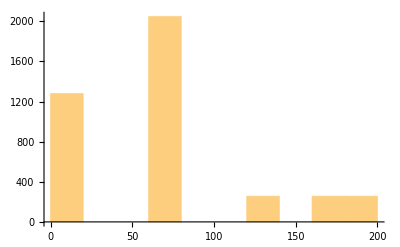

```mathematica
Histogram[lts/.-Infinity->0]
```

```mathematica
SeedRandom[556981];
FeatureSpacePlot[PlotCA/@RandomSample[cas, UpTo[50]]]
```

-Graphics-

## Clinical Trial on Big Yellow

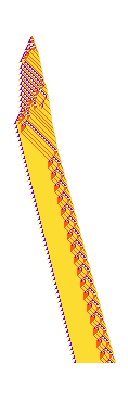

```mathematica
PlotCA@ cas[[10]]
```

```mathematica
idxs = Position[cas, cas[[10]]];
```

```mathematica
heals = gethealers[quickneutral[ru][[idxs[[1, 1]]]], cps[[10]], (#>= 180 &), 200];
```

```mathematica
SeedRandom[333555];
tcas = PerturbPopulation[cas[[idxs[[All, 1]]]],nrus[[idxs[[All, 1]]]], RandomChoice[heals]];
```

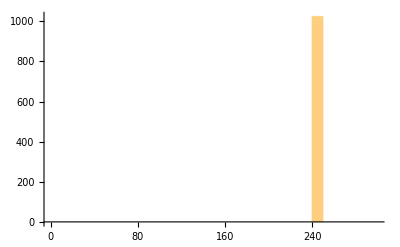

```mathematica
Histogram[(tlts = TestCALifeTime/@ tcas)/.-Infinity->0, {10}, PlotRange->{{0, 200}, {0, Length[idxs]}}]
```

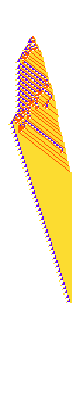
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PlotCA/@ RandomSample[tcas, UpTo[50]]
```

## Population Disease Response on Other Rules

```mathematica
Length/@(quickneutral/@ k4rob[[All, 1]])
```

{1024,1,1024,1,4,1,64,4,16,1,65536,64,64,64,16,16,4,1,1024,4,1,1,4,4096,1,1,1,4,4,1}

```mathematica
ru2 = k4rob[[11, 1]];
```

```mathematica
cps =getcancerperts[ru2];
```

```mathematica
nrus = RandomSample[quickneutral[ru2], 1000];
```

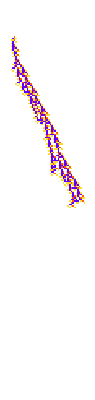

```mathematica
PlotCA[ru2]
```

```mathematica
SeedRandom[556982];
c = RandomChoice[cps];
lts = TestCALifeTime/@(cas = PerturbPopulation[nrus, c]);
```

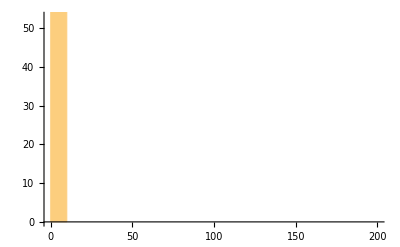

```mathematica
Histogram[lts/.-Infinity->0,  {10}, PlotRange->{{0, 200}, {0, Length[idxs]}}]
```

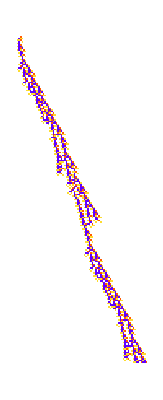
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PlotCA/@ cas[[-10;;]]
```

```mathematica
SeedRandom[556981];
FeatureSpacePlot[PlotCA/@RandomSample[cas, UpTo[50]]]
```

-Graphics-

## Clinical Trial on Other Rule

```mathematica
PlotCA@ cas[[3]]
```

-Graphics-

```mathematica
idxs = Position[cas, cas[[11]]];
```

```mathematica
idxs = Table[{i}, {i, Length[cas]}];
```

```mathematica
heals = gethealers[nrus[[idxs[[1, 1]]]], c, (#>= 100&&#<= 110 &), 200];
```

```mathematica
SeedRandom[333557];
tcas = PerturbPopulation[cas[[idxs[[All, 1]]]],nrus[[idxs[[All, 1]]]], Echo@RandomChoice[heals]];
```

97→{{13},Enumerate,AddValue→1}

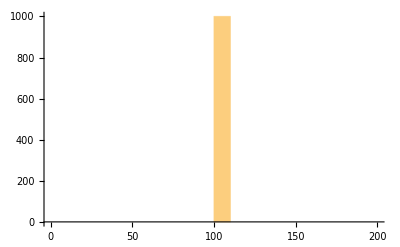

```mathematica
Histogram[(tlts = TestCALifeTime/@ tcas)/.-Infinity->0, {10}, PlotRange->{{0, 200}, {0, Length[idxs]}}]
```

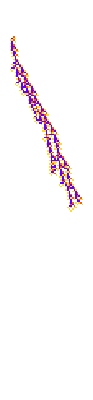
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PlotCA/@ RandomSample[tcas, UpTo[50]]
```